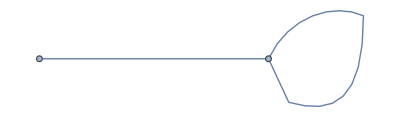

```mathematica
(* Matches (46) of paper *)
G =Graph[{1 <->1, 1 <->2}]
```



```mathematica
(* Matches (57) of paper*)
G=Graph[{1 <->2, 1 <->3, 1 <->4}]
```

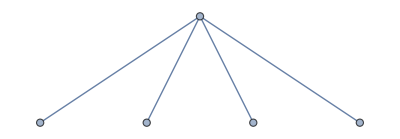

```mathematica
G=Graph[{1 <->2, 1 <->3, 1 <->4, 1 <->5}]
```

```mathematica
G = Graph[{1 <->2, 1<->2}]
```

-Graphics-

```mathematica
G = Graph[{1 <->2, 1<->2, 2<->3, 1<->3}]
```

-Graphics-

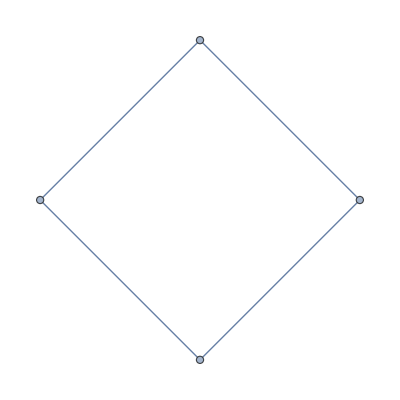

```mathematica
G = Graph[{1 <->2, 2 <->3, 3<->4, 4<->1}]
```

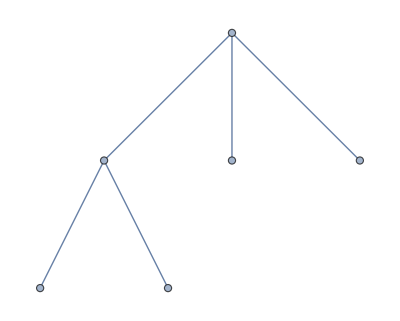

```mathematica
G = Graph[{1 <->2, 1 <->3, 1<->4, 2<->5, 2<->6}]
```

```mathematica
G = Graph[{1 <->2, 1 <->2, 1<->2, 1<->2}]
```

-Graphics-

```mathematica
G = Graph[{1 <->2, 1 <->2, 2<->4, 1<->3}]
```

-Graphics-

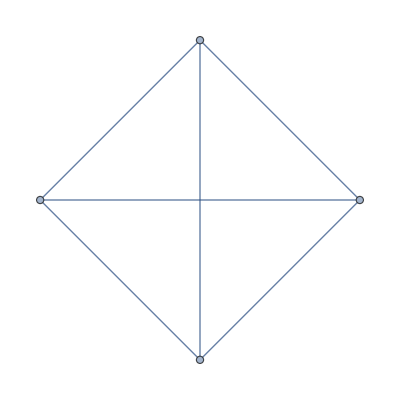

```mathematica
G =Graph[{1 <->2, 1 <->3, 3<->2, 1<->4, 2<->4, 3<->4}]
```

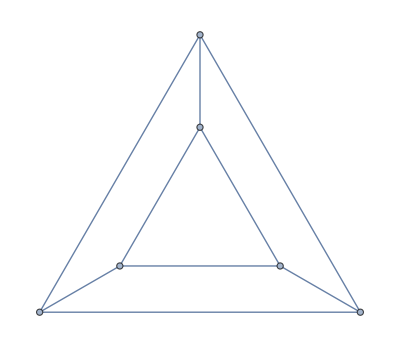

```mathematica
G = PetersenGraph[3,1]
```

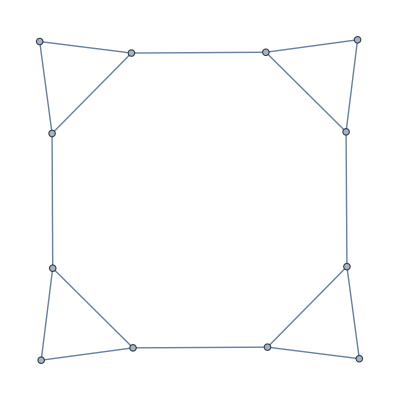

```mathematica
G = Graph[{1 <->2, 1 <->3, 2<->3,2 <->4, 3 <->5, 4<->6,4 <->7, 5 <->8, 5<->9, 6 <->7, 7 <->10, 8<->9, 9 <->11, 10<->11,10 <->12, 11 <->12}]
```

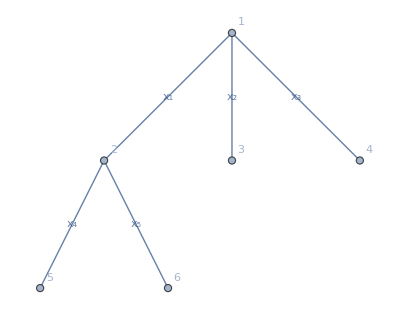

(0 | 0 | 0 | 0 | 0 | -1/3 | 2/3 | 2/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/3 | -1/3 | 2/3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2/3 | 2/3 | -1/3 | 0 | 0
2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/3 | 2/3
2/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | -1/3
-1/3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2/3 | 2/3
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* The below code will output the bond scattering matrix for the above compiled graph *)
V = VertexList[G];
Es= EdgeList[G];
De[i_] := Which[2∣i, Reverse[Es[[i/2]]],!2∣i, Es[[(i + 1)/2]]]
dv[j_] := VertexDegree[G, De[j][[2]]]

sign[i_,j_]:=Which[
Ceiling[i/2]==Ceiling[j/2] && i  ≠ j,  2/ dv[j]  - 1,
De[i][[1]] == De[j][[2]] ,  2/ dv[j] ,
True, 0]

M = Table[sign[i,j], {i,2 Length[Es]},{j,2 Length[Es]}];
(* This formats the matrix where each odd numbered cols/rows is proceeded by the col/row corresponding to opposite oriented edge copy. As in (46) of paper.*)
M//MatrixForm;

reversed=Table[2*x, {x,Range[Length[Es]]}];
edges = Table[2*x-1, {x,Range[Length[Es]]}];
ord = Join[edges,reversed];
(* This formats the matrix where first |E| cols/rows corespond to edges in one orientation and last |E| cols/rows correspond to edges copies in opposite orientation. As in (57) of paper*)
S = M[[ord,ord]];
Show[SetProperty[SetProperty[G,EdgeLabels->Table[Es[[i]] -> Subscript[x, i], {i,1,Length[Es]}]],VertexLabels->"Name"]]
S // MatrixForm
```

```mathematica
(* Outputs Secular determinant *)
(*Di= DiagonalMatrix[Join[Table[Subscript[x, i], {i,Range[Length[Es]]}],Table[Subscript[x, i], {i,Range[Length[Es]]}]]];*)
Di= DiagonalMatrix[Table[Subscript[x, i], {i,Range[2*Length[Es]]}]];
IdentityMatrix[2*Length[Es]] - S. Di // MatrixForm
(* pe is the resulting polynomial of not identifying both copies of edges *)
pe= Expand[Det[IdentityMatrix[2*Length[Es]] - S. Di]]
p = pe /. Table[Subscript[x, i + Length[Es]]-> Subscript[x, i],{i,1,Length[Es]}];
p
(* p is the secular determinant*)
```

(1 | 0 | 0 | 0 | 0 | x_6/3 | -(2 x_7)/3 | -(2 x_8)/3 | 0 | 0
0 | 1 | 0 | 0 | 0 | -(2 x_6)/3 | x_7/3 | -(2 x_8)/3 | 0 | 0
0 | 0 | 1 | 0 | 0 | -(2 x_6)/3 | -(2 x_7)/3 | x_8/3 | 0 | 0
-(2 x_1)/3 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | x_9/3 | -(2 x_10)/3
-(2 x_1)/3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -(2 x_9)/3 | x_10/3
x_1/3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -(2 x_9)/3 | -(2 x_10)/3
0 | -x_2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | -x_3 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | -x_4 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -x_5 | 0 | 0 | 0 | 0 | 1)

1-(x_1 x_6)/9+(x_2 x_7)/3+1/9 x_1 x_2 x_6 x_7+(x_3 x_8)/3+1/9 x_1 x_3 x_6 x_8-1/3 x_2 x_3 x_7 x_8+1/3 x_1 x_2 x_3 x_6 x_7 x_8+(x_4 x_9)/3+1/9 x_1 x_4 x_6 x_9+1/9 x_2 x_4 x_7 x_9-1/9 x_1 x_2 x_4 x_6 x_7 x_9+1/9 x_3 x_4 x_8 x_9-1/9 x_1 x_3 x_4 x_6 x_8 x_9-1/9 x_2 x_3 x_4 x_7 x_8 x_9-1/3 x_1 x_2 x_3 x_4 x_6 x_7 x_8 x_9+(x_5 x_10)/3+1/9 x_1 x_5 x_6 x_10+1/9 x_2 x_5 x_7 x_10-1/9 x_1 x_2 x_5 x_6 x_7 x_10+1/9 x_3 x_5 x_8 x_10-1/9 x_1 x_3 x_5 x_6 x_8 x_10-1/9 x_2 x_3 x_5 x_7 x_8 x_10-1/3 x_1 x_2 x_3 x_5 x_6 x_7 x_8 x_10-1/3 x_4 x_5 x_9 x_10+1/3 x_1 x_4 x_5 x_6 x_9 x_10-1/9 x_2 x_4 x_5 x_7 x_9 x_10-1/3 x_1 x_2 x_4 x_5 x_6 x_7 x_9 x_10-1/9 x_3 x_4 x_5 x_8 x_9 x_10-1/3 x_1 x_3 x_4 x_5 x_6 x_8 x_9 x_10+1/9 x_2 x_3 x_4 x_5 x_7 x_8 x_9 x_10-x_1 x_2 x_3 x_4 x_5 x_6 x_7 x_8 x_9 x_10

1-x_1^2/9+x_2^2/3+1/9 x_1^2 x_2^2+x_3^2/3+1/9 x_1^2 x_3^2-1/3 x_2^2 x_3^2+1/3 x_1^2 x_2^2 x_3^2+x_4^2/3+1/9 x_1^2 x_4^2+1/9 x_2^2 x_4^2-1/9 x_1^2 x_2^2 x_4^2+1/9 x_3^2 x_4^2-1/9 x_1^2 x_3^2 x_4^2-1/9 x_2^2 x_3^2 x_4^2-1/3 x_1^2 x_2^2 x_3^2 x_4^2+x_5^2/3+1/9 x_1^2 x_5^2+1/9 x_2^2 x_5^2-1/9 x_1^2 x_2^2 x_5^2+1/9 x_3^2 x_5^2-1/9 x_1^2 x_3^2 x_5^2-1/9 x_2^2 x_3^2 x_5^2-1/3 x_1^2 x_2^2 x_3^2 x_5^2-1/3 x_4^2 x_5^2+1/3 x_1^2 x_4^2 x_5^2-1/9 x_2^2 x_4^2 x_5^2-1/3 x_1^2 x_2^2 x_4^2 x_5^2-1/9 x_3^2 x_4^2 x_5^2-1/3 x_1^2 x_3^2 x_4^2 x_5^2+1/9 x_2^2 x_3^2 x_4^2 x_5^2-x_1^2 x_2^2 x_3^2 x_4^2 x_5^2

```mathematica
pa = pe /. Subscript[x, 1]->Subscript[x, 1] z /. Subscript[x, Length[Es]+1]-> Subscript[x, 1] z^(-1)/. Table[Subscript[x, i + Length[Es]]-> Subscript[x, i],{i,2,Length[Es]}];
FullSimplify[pa]
```

1/9 ((-3-x_3^2+x_2^2 (-1+x_3^2)) (-3-x_5^2+x_4^2 (-1+x_5^2))-x_1^2 (-1+x_3^2+x_2^2 (1+3 x_3^2)) (-1+x_5^2+x_4^2 (1+3 x_5^2)))

```mathematica
L =.
L = Sum[Subscript[θ, k],{k,Length[Es]}];
Pa = pa /. z-> Exp[I Subscript[α, 1]] /. Table[Subscript[x, k] -> Exp[I Subscript[θ, k]], {k,1,Length[Es]}] /. Table[Subscript[x, k] -> Exp[I Subscript[θ, k-Length[Es]] ], {k,Length[Es] + 1,2Length[Es]}]
FullSimplify[Pa]
```

1-1/9 ⅇ^(2 ⅈ θ_1)+1/9 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_2)+1/3 ⅇ^(2 ⅈ θ_2)+1/9 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_3)-1/3 ⅇ^(2 ⅈ θ_2+2 ⅈ θ_3)+1/3 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_2+2 ⅈ θ_3)+1/3 ⅇ^(2 ⅈ θ_3)+1/9 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_4)+1/9 ⅇ^(2 ⅈ θ_2+2 ⅈ θ_4)-1/9 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_2+2 ⅈ θ_4)+1/9 ⅇ^(2 ⅈ θ_3+2 ⅈ θ_4)-1/9 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_3+2 ⅈ θ_4)-1/9 ⅇ^(2 ⅈ θ_2+2 ⅈ θ_3+2 ⅈ θ_4)-1/3 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_2+2 ⅈ θ_3+2 ⅈ θ_4)+1/3 ⅇ^(2 ⅈ θ_4)+1/9 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_5)+1/9 ⅇ^(2 ⅈ θ_2+2 ⅈ θ_5)-1/9 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_2+2 ⅈ θ_5)+1/9 ⅇ^(2 ⅈ θ_3+2 ⅈ θ_5)-1/9 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_3+2 ⅈ θ_5)-1/9 ⅇ^(2 ⅈ θ_2+2 ⅈ θ_3+2 ⅈ θ_5)-1/3 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_2+2 ⅈ θ_3+2 ⅈ θ_5)-1/3 ⅇ^(2 ⅈ θ_4+2 ⅈ θ_5)+1/3 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_4+2 ⅈ θ_5)-1/9 ⅇ^(2 ⅈ θ_2+2 ⅈ θ_4+2 ⅈ θ_5)-1/3 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_2+2 ⅈ θ_4+2 ⅈ θ_5)-1/9 ⅇ^(2 ⅈ θ_3+2 ⅈ θ_4+2 ⅈ θ_5)-1/3 ⅇ^(2 ⅈ θ_1+2 ⅈ θ_3+2 ⅈ θ_4+2 ⅈ θ_5)+1/9 ⅇ^(2 ⅈ θ_2+2 ⅈ θ_3+2 ⅈ θ_4+2 ⅈ θ_5)-ⅇ^(2 ⅈ θ_1+2 ⅈ θ_2+2 ⅈ θ_3+2 ⅈ θ_4+2 ⅈ θ_5)+1/3 ⅇ^(2 ⅈ θ_5)

8/9 ⅈ ⅇ^(ⅈ (θ_1+θ_2+θ_3+θ_4+θ_5)) (-Cos[θ_5] (-Sin[θ_1-θ_2-θ_3+θ_4]+Sin[θ_1+θ_2-θ_3+θ_4]+Sin[θ_1-θ_2+θ_3+θ_4]+3 Sin[θ_1+θ_2+θ_3+θ_4])+4 Cos[θ_4] (-Cos[θ_2] Cos[θ_1+θ_3]+Cos[θ_3] Sin[θ_1] Sin[θ_2]) Sin[θ_5])

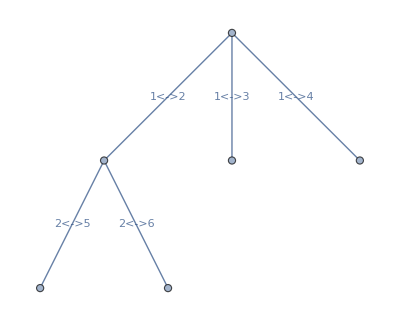

Unset::norep: Assignment on Subscript for l_1 not found.

Unset::norep: Assignment on Subscript for l_2 not found.

Unset::norep: Assignment on Subscript for l_3 not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

-2/9 (4 Cos[t l_5] (-Sin[t (l_1-l_2-l_3+l_4)]+Sin[t (l_1+l_2-l_3+l_4)]+Sin[t (l_1-l_2+l_3+l_4)]+3 Sin[t (l_1+l_2+l_3+l_4)])+16 Cos[t l_4] (Cos[t l_2] Cos[t (l_1+l_3)]-Cos[t l_3] Sin[t l_1] Sin[t l_2]) Sin[t l_5])

```mathematica
(* Computing effects of magnetic flux α on edge 1 -> 2 at kth Eigenvalue.*)
Show[SetProperty[G,EdgeLabels->"Name"],PlotRange->All]

For[k= 1, k ≤ Length[Es], k++, Unset[Subscript[l, k] ]];
L = Sum[Subscript[l, k], {k,1,Length[Es]}];
Pa =.;
Pa[t,α] := Exp[-I t L]/ Sqrt[Det[S]]  pe /. Subscript[x, 1]-> Exp[I Subscript[l, 1] (t + α)] /. Subscript[x, Length[Es] + 1]-> Exp[I Subscript[l, 1] (t - α)]/. Table[Subscript[x, k] -> Exp[I Subscript[l, k] t], {k,2,Length[Es]}] /. Table[Subscript[x, k] -> Exp[I Subscript[l, k - Length[Es]] t], {k,Length[Es] + 2,2Length[Es]}]
Pa[t_,α_] = FullSimplify[Pa[t,α]]
```

-Graphics-

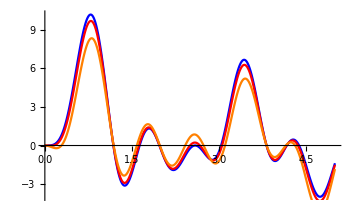

```mathematica
(* This is the FullReduced Secular Determinant for the following Graph *)
G = Graph[{1 <->2, 1 <->2, 1<->2, 1<->2}]
r = 5;
Subscript[l, 1] = 1; Subscript[l, 2] = Sqrt[2]; Subscript[l, 3] = Sqrt[3]; Subscript[l, 4] = Pi; Subscript[l, 5] = Sqrt[2] Pi; Subscript[l, 6] = Pi^2;
Pa=.;
Pa[t_,α_] = Cos[t (Subscript[l, 1]-Subscript[l, 2])]-Cos[t (Subscript[l, 1]+Subscript[l, 2])]+Cos[t (Subscript[l, 1]-Subscript[l, 3])]-Cos[t (Subscript[l, 1]+Subscript[l, 3])]+Cos[t (Subscript[l, 1]-Subscript[l, 4])]-1/2 Cos[t (Subscript[l, 1]-Subscript[l, 2]-Subscript[l, 3]-Subscript[l, 4])]-1/2 Cos[t (Subscript[l, 1]+Subscript[l, 2]+Subscript[l, 3]-Subscript[l, 4])]-Cos[t (Subscript[l, 1]+Subscript[l, 4])]-1/2 Cos[t (Subscript[l, 1]+Subscript[l, 2]-Subscript[l, 3]+Subscript[l, 4])]-1/2 Cos[t (Subscript[l, 1]-Subscript[l, 2]+Subscript[l, 3]+Subscript[l, 4])]+2 (Cos[t (Subscript[l, 1]+Subscript[l, 2]+Subscript[l, 3]+Subscript[l, 4])]+Cos[α Subscript[l, 1]] (Sin[t Subscript[l, 3]] Sin[t Subscript[l, 4]]+Sin[t Subscript[l, 2]] (Sin[t Subscript[l, 3]]+Sin[t Subscript[l, 4]])));

Show[Plot[Pa[t,0], {t,0,r}, PlotStyle -> Blue, MaxRecursion-> 1, PlotPoints-> 1000],
Plot[Pa[t,.5], {t,0,r}, PlotStyle -> Red, MaxRecursion-> 1, PlotPoints-> 1000],
Plot[Pa[t,1], {t,0,r}, PlotStyle -> Orange, MaxRecursion-> 1, PlotPoints-> 1000]]
ContourPlot[Pa[t,α],{t, 0,r}, {α, -3.14,3.14}, MaxRecursion-> 2, PlotPoints-> 100]
```

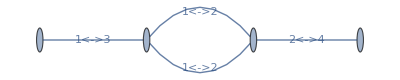

(z (9+2 x_1^2+x_1^4)-4 (1+z^2) (x_1+x_1^3) x_2+2 z (1+x_1^2)^2 x_2^2-4 (1+z^2) (x_1+x_1^3) x_2^3+z (1+2 x_1^2+9 x_1^4) x_2^4)/(9 z)

Unset::norep: Assignment on Subscript for l_1 not found.

$Failed

Unset::norep: Assignment on Subscript for l_2 not found.

$Failed

2/9 ⅇ^(2 ⅈ t (l_1+l_2)) (2+2 Cos[2 t l_1]-4 Cos[t (α-l_1-l_2)]+Cos[2 t (l_1-l_2)]-4 Cos[t (α+l_1-l_2)]+2 Cos[2 t l_2]-4 Cos[t (α-l_1+l_2)]+9 Cos[2 t (l_1+l_2)]-4 Cos[t (α+l_1+l_2)])

```mathematica
(* Here we plot the flux of the following graph with the lengths of the 1st and 3rd  edges having the same length as well as the lengths of the 2nd and 4th edges *)
G = Graph[{1 <->2, 1 <->2, 2<->4, 1<->3}];
Show[SetProperty[G,EdgeLabels->"Name"],PlotRange->All]
pe = 1/729 (729-81 Subscript[x, 1] Subscript[x, 5]-324 Subscript[x, 2] Subscript[x, 5]-324 Subscript[x, 1] Subscript[x, 6]-81 Subscript[x, 2] Subscript[x, 6]+81 Subscript[x, 1] Subscript[x, 2] Subscript[x, 5] Subscript[x, 6]+243 Subscript[x, 3] Subscript[x, 7]+81 Subscript[x, 1] Subscript[x, 3] Subscript[x, 5] Subscript[x, 7]-324 Subscript[x, 2] Subscript[x, 3] Subscript[x, 5] Subscript[x, 7]-324 Subscript[x, 1] Subscript[x, 3] Subscript[x, 6] Subscript[x, 7]+81 Subscript[x, 2] Subscript[x, 3] Subscript[x, 6] Subscript[x, 7]+243 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3] Subscript[x, 5] Subscript[x, 6] Subscript[x, 7]+243 Subscript[x, 4] Subscript[x, 8]+81 Subscript[x, 1] Subscript[x, 4] Subscript[x, 5] Subscript[x, 8]-324 Subscript[x, 2] Subscript[x, 4] Subscript[x, 5] Subscript[x, 8]-324 Subscript[x, 1] Subscript[x, 4] Subscript[x, 6] Subscript[x, 8]+81 Subscript[x, 2] Subscript[x, 4] Subscript[x, 6] Subscript[x, 8]+243 Subscript[x, 1] Subscript[x, 2] Subscript[x, 4] Subscript[x, 5] Subscript[x, 6] Subscript[x, 8]+81 Subscript[x, 3] Subscript[x, 4] Subscript[x, 7] Subscript[x, 8]-81 Subscript[x, 1] Subscript[x, 3] Subscript[x, 4] Subscript[x, 5] Subscript[x, 7] Subscript[x, 8]-324 Subscript[x, 2] Subscript[x, 3] Subscript[x, 4] Subscript[x, 5] Subscript[x, 7] Subscript[x, 8]-324 Subscript[x, 1] Subscript[x, 3] Subscript[x, 4] Subscript[x, 6] Subscript[x, 7] Subscript[x, 8]-81 Subscript[x, 2] Subscript[x, 3] Subscript[x, 4] Subscript[x, 6] Subscript[x, 7] Subscript[x, 8]+729 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3] Subscript[x, 4] Subscript[x, 5] Subscript[x, 6] Subscript[x, 7] Subscript[x, 8]);

P = pe /.Subscript[x, 1]->Subscript[x, 1] z /. Subscript[x, 5]->Subscript[x, 1] z^(-1) /. Table[Subscript[x, 4+k]-> Subscript[x, k],{k,2, 4}];
P = P/.Subscript[x, 3]->Subscript[x, 1] /. Subscript[x, 4]->Subscript[x, 2];
P = FullSimplify[P]
z =.
Subscript[l, 1] =.
Subscript[l, 2]=.
Ps = FullSimplify[P /. Subscript[x, 1]-> Exp[I Subscript[l, 1] t] /. Subscript[x, 2]-> Exp[I Subscript[l, 2] t]/. z-> Exp[I α t]]
```

```mathematica
S= ContourPlot3D[2 (Cos[Subscript[α, 1]]-Cos[Subscript[θ, 1]]) Cos[Subscript[θ, 2]]+Sin[Subscript[θ, 1]] Sin[Subscript[θ, 2]]==0,{Subscript[θ, 1],0,2Pi},{Subscript[θ, 2],0,2Pi},{Subscript[α, 1],-Pi,Pi}];
```

```mathematica
Show[S, ContourPlot3D[Subscript[α, 1]==0,{Subscript[θ, 1],0,10},{Subscript[θ, 2],0,10},{Subscript[α, 1],-3,3}], ParametricPlot3D[{ Mod[t,2Pi],Mod[Sqrt[2]t,2Pi],0},{t,0,10}],ContourPlot3D[Sqrt[2] Subscript[θ, 1]==Subscript[θ, 2],{Subscript[θ, 1],0,2Pi},{Subscript[θ, 2],0,2Pi},{Subscript[α, 1],-3,3}, ContourStyle->Blue]]
```

-Graphics3D-

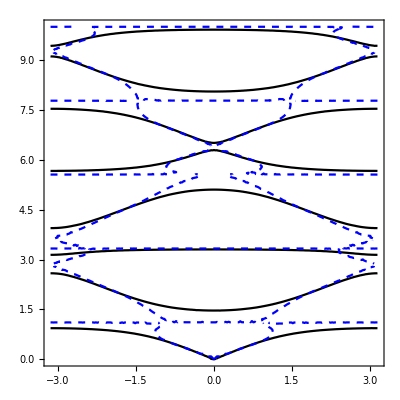

```mathematica
F = 2 (Cos[Subscript[α, 1]]-Cos[t]) Cos[Sqrt[2]t]+Sin[t] Sin[Sqrt[2]t];
dFda= D[F,Subscript[α, 1]];
dFda2= D[dFda,Subscript[α, 1]];
dFdt = D[F,t];
dFdt2 = D[dFdt,t];
dFdadt = D[dFdt,Subscript[α, 1]];
dtda = -dFda/dFdt;
dtda2 = -(dFda2 + (dFdadt + dFdt2 dtda)dtda)/dFdt;
(*FullSimplify[dtda2]*)
dtda2 = -(Cos[√2 t] (-2 Cos[Subscript[α, 1]] ((2+√2) Cos[√2 t] Sin[t]+(Cos[t]+2 √2 Cos[t]-2 √2 Cos[Subscript[α, 1]]) Sin[√2 t])^2+((20+6 √2) Cos[t]-(-1+√2) Cos[t-2 √2 t]+3 (1+√2) Cos[t+2 √2 t]-16 Cos[Subscript[α, 1]]) Sin[Subscript[α, 1]]^2))/((2+√2) Cos[√2 t] Sin[t]+(Cos[t]+2 √2 Cos[t]-2 √2 Cos[Subscript[α, 1]]) Sin[√2 t])^3;
Show[ContourPlot[F==0,{Subscript[α, 1],-Pi,Pi},{t,0,10},ContourStyle->{Black,Bold}],ContourPlot[dtda2 == 0,{Subscript[α, 1],-Pi,Pi},{t,0,10}, ContourStyle->{Blue, Dashed}]]
```

```mathematica
P = 2 (Cos[Subscript[α, 1]]-Cos[Subscript[θ, 1]]) Cos[Subscript[θ, 2]]+Sin[Subscript[θ, 1]] Sin[Subscript[θ, 2]];
H = Table[D[P, i,j], {i, {Subscript[θ, 1],Subscript[θ, 2],Subscript[α, 1]}},{j, {Subscript[θ, 1],Subscript[θ, 2],Subscript[α, 1]}}];
H //MatrixForm

dtda = FullSimplify[- (D[P,Subscript[α, 1]])/(Subscript[θ, 1] D[P,Subscript[θ, 1]] + Subscript[θ, 2] D[P,Subscript[θ, 2]])];
v = {{Subscript[θ, 1] dtda}, {Subscript[θ, 2] dtda}, {1}};
v //MatrixForm


dtda2 = FullSimplify[ (D[P,{Subscript[α, 1],2}])/(Subscript[θ, 1] D[P,Subscript[θ, 1]] + Subscript[θ, 2] D[P,Subscript[θ, 2]])];
dtda2
```

(2 Cos[θ_1] Cos[θ_2]-Sin[θ_1] Sin[θ_2] | Cos[θ_1] Cos[θ_2]-2 Sin[θ_1] Sin[θ_2] | 0
Cos[θ_1] Cos[θ_2]-2 Sin[θ_1] Sin[θ_2] | -2 (Cos[α_1]-Cos[θ_1]) Cos[θ_2]-Sin[θ_1] Sin[θ_2] | 2 Sin[α_1] Sin[θ_2]
0 | 2 Sin[α_1] Sin[θ_2] | -2 Cos[α_1] Cos[θ_2])

((2 Sin[α_1] θ_1)/(Sin[θ_1] (2 θ_1+θ_2)+(-2 Cos[α_1] θ_2+Cos[θ_1] (θ_1+2 θ_2)) Tan[θ_2])
(2 Sin[α_1] θ_2)/(Sin[θ_1] (2 θ_1+θ_2)+(-2 Cos[α_1] θ_2+Cos[θ_1] (θ_1+2 θ_2)) Tan[θ_2])
1)

-(2 Cos[α_1] Cos[θ_2])/((2 Cos[θ_2] Sin[θ_1]+Cos[θ_1] Sin[θ_2]) θ_1+(Cos[θ_2] Sin[θ_1]+2 (-Cos[α_1]+Cos[θ_1]) Sin[θ_2]) θ_2)

```mathematica
S1= ContourPlot3D[2 (Cos[Subscript[α, 1]]-Cos[Subscript[θ, 1]]) Cos[Subscript[θ, 2]]+Sin[Subscript[θ, 1]] Sin[Subscript[θ, 2]]==0,{Subscript[θ, 1],0,2Pi},{Subscript[θ, 2],0,2Pi},{Subscript[α, 1],-Pi,Pi}];
S2= ContourPlot3D[2 Cos[Subscript[α, 1]] Cos[Subscript[θ, 2]]==0,{Subscript[θ, 1],0,2Pi},{Subscript[θ, 2],0,2Pi},{Subscript[α, 1],-Pi,Pi}, ContourStyle->Opacity[0.4]];
```

```mathematica
Show[S1, S2,ContourPlot3D[Subscript[α, 1]==0,{Subscript[θ, 1],0,2Pi},{Subscript[θ, 2],0,2Pi},{Subscript[α, 1],-Pi,Pi}, ContourStyle->Blue]]
```

-Graphics3D-

```mathematica
P = 2 (Cos[Subscript[α, 1]]-Cos[Subscript[θ, 1]]) Cos[Subscript[θ, 2]]+Sin[Subscript[θ, 1]] Sin[Subscript[θ, 2]]/. Subscript[α, 1]-> 0;
S1= ContourPlot[P==0,{Subscript[θ, 1],0,2Pi},{Subscript[θ, 2],0,2Pi}, ContourStyle->Black];
F=2 Cos[Subscript[α, 1]] Cos[Subscript[θ, 2]]/. Subscript[α, 1]-> 0;
S2= RegionPlot[F >= 0,{Subscript[θ, 1], 0, 2Pi},{Subscript[θ, 2],0,2Pi}, MaxRecursion-> 2, PlotPoints->400,  PlotStyle->{Blue}];
```

```mathematica
Show[S2,S1]
```

-Graphics-

```mathematica
Simplify[(x+1)(y+1)^2((-I y + I)/(y+1)((-I x + I)/(x+1) + (-I y + I)/(y+1)) - 4)]
```

-2 (3+3 y+2 y^2+x (2+3 y+3 y^2))

```mathematica
Expand[-2 (3+3 y+2 y^2+x (2+3 y+3 y^2))]
```

-6-4 x-6 y-6 x y-4 y^2-6 x y^2